7.91917

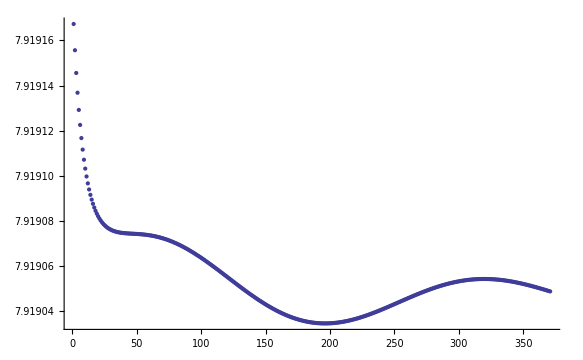

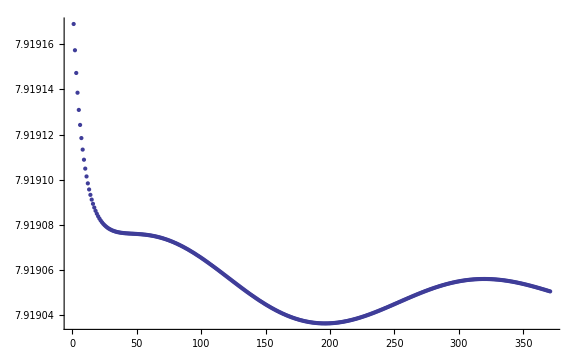

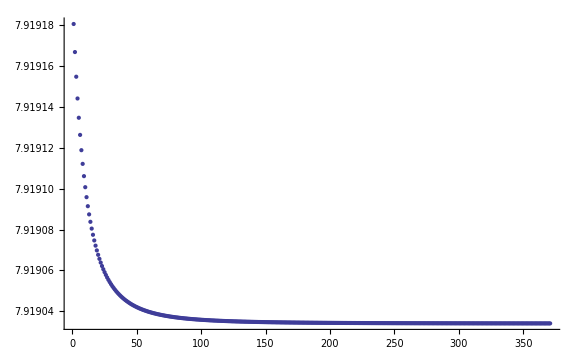

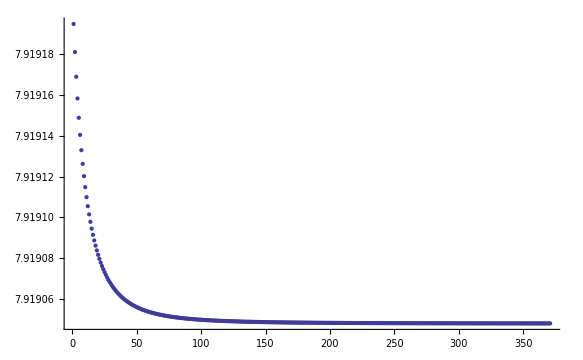

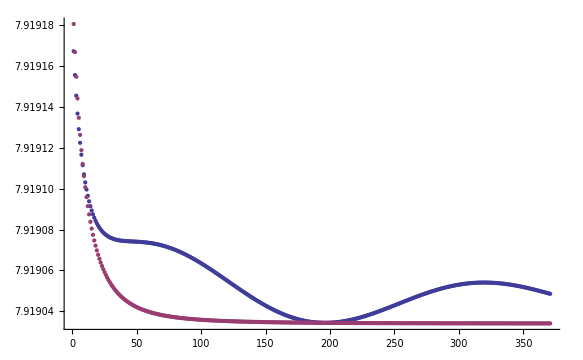

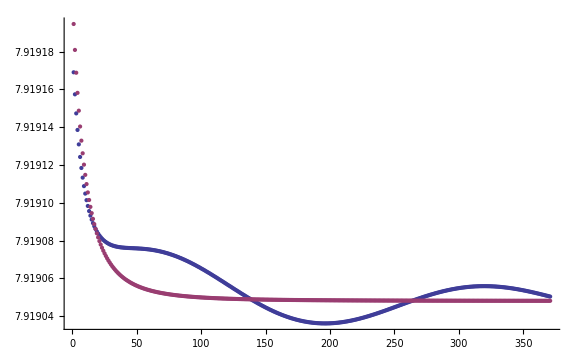

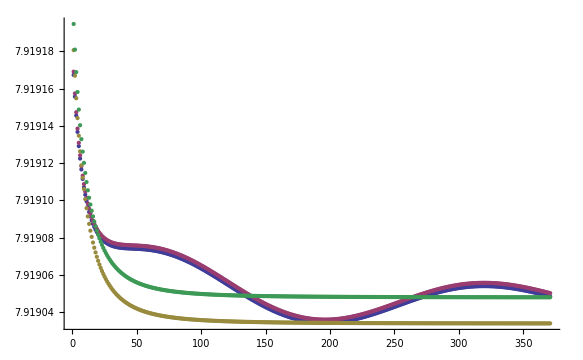

```mathematica
(* Clear all data before calculations *)
Clear[x, r12, r21, r34, r43, z, r13, r31, r24, r42, diag, r14, r41, r23, r32, clight, ωp, fp, γ, sol, M];


(* Geometry parameters of ellipsoid *)
Clear[a, b, c, V, L1];
a = 50; (* 1/2 Length *)
b = 25; (* 1/2 Width *)
c = 15;  (* 1/2 Height *)
V = N[4/3 π a b c]
L1 = NIntegrate[a b c / (2 (s+ a^2 )^(3/2) (s + b^2)^(1/2) (s + c^2)^(1/2)), {s, 0, Infinity}]

(* Length of nanorods *)
x = 100;
r12 = x;
r21 = x;
r34 = x;
r43 = x;

(* Distance btw nanorods *)
z = 30;
r13 = z;
r31 = z;
r24 = z;
r42 = z;

(* Diagonal distance btw dipoles *)
diag = Sqrt[x^2 + z^2];
r14 = diag;
r41 = diag;
r23 = diag;
r32 = diag;

(* Constants *) (* nm/fs *)
clight = 300;
fp =2.183; 
ωp = 2π fp;
a = 1;
r = 100;
γ =0 *6.46*10^(-3);


(* Drude model & phys functions *)
ϵ[ω_] := 1- ωp^2/(ω^2+ ⅈ γ ω);
α[ω_] := (ϵ[ω] - 1)/(ϵ[ω]+2) a^3; 
k[ω_] :=ω/clight ;

(* Define tensor components *)

χ12[ω_] := Exp[ⅈ k[ω] r12] /r12 * (-2 ⅈ k[ω] /r12 + 2/r12^2); (* Parallel Ox *)
χ13[ω_] := Exp[ⅈ k[ω] r13] /r13 * (k[ω]^2 + ⅈ k[ω] /r13 - 1/r13^2); (* Parallel Oz *)
χ14[ω_] :=  Exp[ⅈ k[ω] r14]  (1/r14 * (k[ω]^2 + ⅈ k[ω] /r14 - 1/r14^2) - x^2/r14^3 (k[ω]^2 + ⅈ 3 k[ω] /r14  -3/r14^2));(* Diagonal Ox, Oz *)

χ21[ω_] := Exp[ⅈ k[ω] r21] /r21 * (-2 ⅈ k[ω] /r21 + 2/r21^2);(* Parallel Ox *)
χ23[ω_] := Exp[ⅈ k[ω] r23]  (1/r23 * (k[ω]^2 + ⅈ k[ω]/r23 - 1/r23^2) - x^2/r23^3 (k[ω]^2 + ⅈ 3 k[ω] /r23  -3/r23^2));
(* Diagonal Ox, Oz *)
χ24[ω_] := Exp[ⅈ k[ω] r24] /r24 * (k[ω]^2 + ⅈ k[ω] /r24 - 1/r24^2); (* Parallel Oz *)

χ31[ω_] := Exp[ⅈ k[ω] r31] /r31 * (k[ω]^2 + ⅈ k[ω] /r31 - 1/r31^2); (* Parallel Oz *)
χ32[ω_] := Exp[ⅈ k[ω] r32]  (1/r32 * (k[ω]^2 + ⅈ k[ω] /r32 - 1/r32^2) - x^2/r32^3 (k[ω]^2 + ⅈ 3 k[ω] /r32  -3/r32^2));
(* Diagonal Ox, Oz *)
χ34[ω_] := Exp[ⅈ k[ω] r34] /r34 * (-2 ⅈ k[ω] /r34 + 2/r34^2); (* Parallel Ox *)

χ41[ω_] := Exp[ⅈ k[ω] r41]  (1/r41 * (k[ω]^2 + ⅈ k[ω] /r41 - 1/r41^2) - x^2/r41^3 (k[ω]^2 + ⅈ 3 k[ω] /r41  -3/r41^2));
(* Diagonal Ox, Oz *)
χ42[ω_] := Exp[ⅈ k[ω] r42] /r42 * (k[ω]^2 + ⅈ k[ω] /r42 - 1/r42^2); (* Parallel Oz *)
χ43[ω_] := Exp[ⅈ k[ω] r43] /r43 * (-2 ⅈ k[ω] /r43 + 2/r43^2); (* Parallel Ox *)

(* Creating matrix and finding resonance frequencies *)
M = {{-1/α[ω], χ12[ω], χ13[ω], χ14[ω]}, {χ21[ω], -1/α[ω], χ23[ω], χ24[ω]}, {χ31[ω], χ32[ω], -1/α[ω], χ34[ω]}, {χ41[ω], χ42[ω], χ43[ω], -1/α[ω]}};


(* +1 +1 +1 +1 *)
FindRoot[-1/α[ω]+ χ12[ω]+ χ13[ω]+ χ14[ω] == 0, {ω, 11}][[1]][[2]];
FindRoot[χ21[ω] - 1/α[ω] + χ23[ω] + χ24[ω] == 0, {ω, 11}][[1]][[2]];
FindRoot[χ31[ω] + χ32[ω] - 1/α[ω] + χ34[ω] == 0, {ω, 11}][[1]][[2]];
sol = FindRoot[ χ41[ω] + χ42[ω] + χ43[ω] - 1/α[ω]== 0, {ω, 11}][[1]][[2]];
w = Abs[sol]

Clear[ω, sol1, sol2, w, z, listY1, listY2, listY, listX];
listX = {};
listY1 = {};
Do[z = i;
r13 = z;
r31 = z;
r24 = z;
r42 = z;
AppendTo[listX, N[z]];
sol1 = FindRoot[-1/α[ω]+ χ12[ω]+ χ13[ω]+ χ14[ω] == 0, {ω,11}][[1]][[2]];
w = Abs[sol1];
AppendTo[listY1, w], {i, 30,400, 1}];
ListPlot[{listY1}, PlotRange -> All]

Clear[ω, sol1, sol2, w, z, listY1d, listY, listX];
listX = {};
listY1d = {};
Do[z = i;
r13 = z;
r31 = z;
r24 = z;
r42 = z;
AppendTo[listX, N[z]];
sol1 = FindRoot[-1/α[ω]+ χ12[ω]*0+ χ13[ω]+ χ14[ω]*0 == 0, {ω,11}][[1]][[2]];
w = Abs[sol1];
AppendTo[listY1d, w], {i, 30,400, 1}];
ListPlot[{listY1d}, PlotRange -> All]

(* Define tensor components *)

χ12[ω_] := 1 /r12 * (0+ 2/r12^2); (* Parallel Ox *)
χ13[ω_] := 1 /r13 * (0 + 0 - 1/r13^2); (* Parallel Oz *)
χ14[ω_] :=  1 (1/r14 * (0 + 0 - 1/r14^2) - x^2/r14^3 (0 + 0  -3/r14^2));(* Diagonal Ox, Oz *)

χ21[ω_] := 1 /r21 * (-2 ⅈ k[ω] /r21 + 2/r21^2);(* Parallel Ox *)
χ23[ω_] := 1  (1/r23 * (0 + 0 - 1/r23^2) - x^2/r23^3 (0 + 0  -3/r23^2));
(* Diagonal Ox, Oz *)
χ24[ω_] :=1 /r24 * (0 + 0 - 1/r24^2); (* Parallel Oz *)

χ31[ω_] := 1 /r31 * (0+ 0 - 1/r31^2); (* Parallel Oz *)
χ32[ω_] :=1  (1/r32 * (0 + 0 - 1/r32^2) - x^2/r32^3 (0+ 0 -3/r32^2));
(* Diagonal Ox, Oz *)
χ34[ω_] := 1 /r34 * (-2 ⅈ k[ω] /r34 + 2/r34^2); (* Parallel Ox *)

χ41[ω_] :=1  (1/r41 * (0 + 0 - 1/r41^2) - x^2/r41^3 (0 +0 -3/r41^2));
(* Diagonal Ox, Oz *)
χ42[ω_] := 1 /r42 * (0 + 0 - 1/r42^2); (* Parallel Oz *)
χ43[ω_] := 1 /r43 * (0 + 2/r43^2); (* Parallel Ox *)

(* +1 +1 +1 +1 *)
FindRoot[-1/α[ω]+ χ12[ω]+ χ13[ω]+ χ14[ω] == 0, {ω, 11}][[1]][[2]];
FindRoot[χ21[ω] - 1/α[ω] + χ23[ω] + χ24[ω] == 0, {ω, 11}][[1]][[2]];
FindRoot[χ31[ω] + χ32[ω] - 1/α[ω] + χ34[ω] == 0, {ω, 11}][[1]][[2]];
sol = FindRoot[ χ41[ω] + χ42[ω] + χ43[ω] - 1/α[ω]== 0, {ω, 11}][[1]][[2]];
w = Abs[sol];

Clear[ω, sol1, sol2, w, z, listY2, listY, listX];
listX = {};
listY2 = {};
Do[z = i;
r13 = z;
r31 = z;
r24 = z;
r42 = z;
AppendTo[listX, N[z]];
sol1 = FindRoot[-1/α[ω]+ χ12[ω]+ χ13[ω]+ χ14[ω] == 0, {ω,11}][[1]][[2]];
w = Abs[sol1];
AppendTo[listY2, w], {i, 30,400, 1}];
ListPlot[{listY2}, PlotRange -> All]


Clear[ω, sol1, sol2, w, z, listY2d, listX];
listX = {};
listY2d = {};
Do[z = i;
r13 = z;
r31 = z;
r24 = z;
r42 = z;
AppendTo[listX, N[z]];
sol1 = FindRoot[-1/α[ω]+ χ12[ω]*0+ χ13[ω]+ χ14[ω]*0 == 0, {ω,11}][[1]][[2]];
w = Abs[sol1];
AppendTo[listY2d, w], {i, 30,400, 1}];
ListPlot[{listY2d}, PlotRange -> All]
ListPlot[{listY1, listY2}, PlotRange -> All]
ListPlot[{listY1d, listY2d}, PlotRange -> All]
ListPlot[{listY1, listY1d, listY2, listY2d}, PlotRange -> All]
```